# Figure 5: Comparing SCSS to GPS Breeding

rOpt is the input squeezing for a GPS state, created by detecting n photons, to have peaks at q =+-Sqrt[2 Pi].

```mathematica
rOpt = 1/2*ArcSech[(2*Pi)/n];
```

The conditional position wave-function that results from breeding two SCSS states (with optimal coherent amplitude, parity κ, squeezing rOpt, and homodyne outcome pTilde) and displacement (δ) in momentum is φκrOptpδ.

```mathematica
φκrOptpδ = Exp[-I*δ*q]*((ⅇ^(-1/2 ⅇ^(2 r) (-2 √π+q)^2)+ⅇ^(-1/2 ⅇ^(2 r) (2 √π+q)^2)+2 ⅇ^(-1/2 ⅇ^(2 r) q^2) Cos[k π+2 √π pTilde])/(√2 π^(1/4) √(ⅇ^-r (2+ⅇ^(-4 ⅇ^(2 r) π)+Cos[4 √π pTilde]+4 ⅇ^(-ⅇ^(2 r) π) Cos[k π+2 √π pTilde]))))/.r->rOpt;
```

Given a κ, r, and pTilde, the optimal corrective displacement is given by δκrOptp

```mathematica
δκrOptp = Arg[(ⅇ^(-5 ⅇ^(2 r) π)+ⅇ^(3 ⅇ^(2 r) π) (5+2 Cos[4 √π pTilde])+4 (1+ⅇ^(4 ⅇ^(2 r) π)) Cos[k π+2 √π pTilde])/(1+ⅇ^(4 ⅇ^(2 r) π) (2+Cos[4 √π pTilde])+4 ⅇ^(3 ⅇ^(2 r) π) Cos[k π+2 √π pTilde])]/(2*√π)/.r->rOpt;
```

Applying δκrOptp toφκrOptpδ

```mathematica
φκrOptpδ/.δ->δκrOptp
```

(ⅇ^(-(ⅈ q Arg[(ⅇ^(-5 ⅇ^ArcSech[(2 π)/n] π)+ⅇ^(3 ⅇ^ArcSech[(2 π)/n] π) (5+2 Cos[4 √π pTilde])+4 (1+ⅇ^(4 ⅇ^ArcSech[(2 π)/n] π)) Cos[k π+2 √π pTilde])/(1+ⅇ^(4 ⅇ^ArcSech[(2 π)/n] π) (2+Cos[4 √π pTilde])+4 ⅇ^(3 ⅇ^ArcSech[(2 π)/n] π) Cos[k π+2 √π pTilde])])/(2 √π)) (ⅇ^(-1/2 ⅇ^ArcSech[(2 π)/n] (-2 √π+q)^2)+ⅇ^(-1/2 ⅇ^ArcSech[(2 π)/n] (2 √π+q)^2)+2 ⅇ^(-1/2 ⅇ^ArcSech[(2 π)/n] q^2) Cos[k π+2 √π pTilde]))/(√2 π^(1/4) √(ⅇ^(-1/2 ArcSech[(2 π)/n]) (2+ⅇ^(-4 ⅇ^ArcSech[(2 π)/n] π)+Cos[4 √π pTilde]+4 ⅇ^(-ⅇ^ArcSech[(2 π)/n] π) Cos[k π+2 √π pTilde])))

The homodyne probability distribution associated with φκrp is Pκrp.

```mathematica
PκrOptp = (ⅇ^(-ⅇ^(-2 r) pTilde^2-r) (1+ⅇ^(4 ⅇ^(2 r) π) (1+2 Cos[2 pTilde √π]^2)+4 ⅇ^(3 ⅇ^(2 r) π) Cos[2 pTilde √π+k π]))/(2 ((-1)^k+ⅇ^(2 ⅇ^(2 r) π))^2 √π)/.r->rOpt
```

(ⅇ^(-ⅇ^(-ArcSech[(2 π)/n]) pTilde^2-1/2 ArcSech[(2 π)/n]) (1+ⅇ^(4 ⅇ^ArcSech[(2 π)/n] π) (1+2 Cos[2 √π pTilde]^2)+4 ⅇ^(3 ⅇ^ArcSech[(2 π)/n] π) Cos[k π+2 √π pTilde]))/(2 ((-1)^k+ⅇ^(2 ⅇ^ArcSech[(2 π)/n] π))^2 √π)

The conditional position wave-function that results from breeding to GPS states (with created from detecting n photons, optimal squeezing,  and homodyne outcome pTilde) and displacement (δ) in momentum is φTildeκrp.

```mathematica
f[n_,k_]:= Exp[-1/2*2 *Pi/n*pTilde^2]*Sum[(-1)^l*Binomial[n,k]*Binomial[2*k,2*l]*((4*Pi^2*pTilde^2)/n^2)^(k-l)*((4*Pi)/n)^(l+1/2)*Gamma[l+1/2],{l,0,2*k}];
φTildenpδ[n_] := (Exp[-1/2*n/(2*Pi)*q^2]Exp[-I*δ*q]*Sum[f[n,k]*(-1)^j *(Pi/n)^(l+j)*(Factorial[2*(n-k)]/(Factorial[2*(n-k-j-l)]*Factorial[l]*Factorial[j]))*q^(2*(n-k-l-j)),{k,0,n},{l,0,2*(n-k)},{j,0,2*(n-k-l)}])/(Sqrt[Sum[f[n,k]*f[n,kPrime]*((2*Pi)/n)^(2*n-k-kPrime+1/2)*Gamma[2*n-k-kPrime+1/2],{k,0,n},{kPrime,0,n}]]);
```

Given a n and pTilde, the optimal corrective displacement is given by δnp

```mathematica
h[n_,l_]:= 2*Exp[-n/2]*Sum[(-1)^(l-j)*Binomial[2*l,2*j]*(n^2/(4*Pi))^(l-j)*(2*Pi)^(-j-1/2)*Gamma[(3+2*j)/2]*n^((2*j+1)/2)1/(1+2*j),{j,0,2*l}];
g[n_,k_,l_]:=(-1)^(n-k+l)*Binomial[2(n-k),2*l]((4*Pi^2)/n^2)^(n-k-l)*((4*Pi)/n)^(l+1/2)*Gamma[l+1/2];
δnp[n_] :=Arg[ Sum[f[n,k]*f[n,kPrime]*g[n,k,l]*g[n,kPrime,lPrime]*h[n,2*n-k-kPrime-l-lPrime],{k,0,n},{l,0,2*(n-k)},{kPrime,0,n},{lPrime,0,2(n-kPrime)}]/(2*Pi*Sum[f[n,k]*f[n,kPrime]*((2*Pi)/n)^(2*n-k-kPrime+1/2)*Gamma[2*n-k-kPrime+1/2],{k,0,n},{kPrime,0,n}])]/2*Sqrt[Pi];
```

The homodyne probability distribution associated with φTildenpδ is PTildenp.

```mathematica
PTildenp[n_]:=(1/Gamma[n+1/2]*(n/(4*Pi))^n*Sqrt[n]/(2*Pi))^2*Sum[f[n,k]*f[n,kPrime]*((2*Pi)/n)^(2*n-k-kPrime+1/2)*Gamma[2*n-k-kPrime+1/2],{kPrime,0,n},{k,0,n}];
```

## Generate Data

Points to get data for the following parameters

```mathematica
nSpace = DeleteCases[DeleteCases[Range[7,40],39],37];
pSpace = Range[0,2*Sqrt[Pi],Sqrt[Pi]/2];
```

Generating Data (Do this on HPC)

```mathematica
(*φTildenpδTable  = ParallelTable[{nSpace[[ii]],Simplify[φTildenpδ[nSpace[[ii]]] ,Assumptions->{pTilde ∈ Reals,q ∈ Reals, δ ∈ Reals}]},{ii,1,Length[nSpace]}];
indx  = Table[Partition[Flatten[Table[{k,l,kPrime,lPrime},{k,0,nSpace[[ii]]},{l,0,2*(nSpace[[ii]]-k)},{kPrime,0,nSpace[[ii]]},{lPrime,0,2(nSpace[[ii]]-kPrime)}]],4],{ii,1,Length[nSpace]}];
γ  = Table[FullSimplify[Total[ParallelTable[f[nSpace[[ii]],indx[[ii,jj,1]]]*f[indx[[ii]],indx[[ii,jj,3]]]*g[nSpace[[ii]],indx[[ii,jj,1]],indx[[ii,jj,2]]]*g[nSpace[[ii]],indx[[ii,jj,3]],indx[[ii,jj,4]]]*h[nSpace[[ii]],2*nSpace[[ii]]-indx[[ii,jj,1]]-indx[[ii,jj,3]]-indx[[ii,jj,2]]-indx[[ii,jj,4]]],{jj,1,Length[indx[[ii]]]}]]],{ii,1,Length[nSpace]}];*)
φTildenpδTable =Get["Figure 5/φTildenpqδTable"];
γ = Get["Figure 5/γ"];
PTildenpTable =ParallelTable[PTildenp[nSpace[[ii]]]/.pTilde->pSpace[[jj]],{ii,1,Length[nSpace]},{jj,1,Length[pSpace]}];
```

```mathematica
γTable = Table[γ[[ii,2]]/.pTilde->pSpace[[jj]],{ii,1,Length[nSpace]},{jj,1, Length[pSpace]}];
δnpTable = Table[Arg[γTable[[ii,jj]]]/(2*Sqrt[Pi]),{ii,1,Length[nSpace]},{jj,1, Length[pSpace]}];
```

Fidelity integrand Table

```mathematica
FidelityIntegrandTable = Table[(ⅇ^(-(-ⅈ q Arg[(ⅇ^(-5 ⅇ^ArcSech[(2 π)/n] π)+ⅇ^(3 ⅇ^ArcSech[(2 π)/n] π) (5+2 Cos[4 √π pTilde])+4 (1+ⅇ^(4 ⅇ^ArcSech[(2 π)/n] π)) Cos[k π+2 √π pTilde])/(1+ⅇ^(4 ⅇ^ArcSech[(2 π)/n] π) (2+Cos[4 √π pTilde])+4 ⅇ^(3 ⅇ^ArcSech[(2 π)/n] π) Cos[k π+2 √π pTilde])])/(2 √π)) (ⅇ^(-1/2 ⅇ^ArcSech[(2 π)/n] (-2 √π+q)^2)+ⅇ^(-1/2 ⅇ^ArcSech[(2 π)/n] (2 √π+q)^2)+2 ⅇ^(-1/2 ⅇ^ArcSech[(2 π)/n] q^2) Cos[k π+2 √π pTilde]))/(√2 π^(1/4) √(ⅇ^(-1/2 ArcSech[(2 π)/n]) (2+ⅇ^(-4 ⅇ^ArcSech[(2 π)/n] π)+Cos[4 √π pTilde]+4 ⅇ^(-ⅇ^ArcSech[(2 π)/n] π) Cos[k π+2 √π pTilde])))*(φTildenpδTable[[ii,2]])/.{k->Mod[nSpace[[ii]],2],pTilde->pSpace[[jj]],δ->δnpTable[[ii,jj]],n->nSpace[[ii]]},{ii,1, Length[nSpace]},{jj,1,Length[pSpace]}];
```

Integrate (Do this on HPC)

```mathematica
(*SSCToGBSpδFidelityTable =ParallelTable[{nSpace[[kk]],pSpace[[jj]],Abs[NIntegrate[FidelityIntegrandTable[[kk,jj]],{q,-∞,∞},Method->"Trapezoidal"]]^2},{kk,1,Length[nSpace]},{jj,1,Length[pSpace]}];*)
SSCToGBSpδFidelityTable =Get["Figure 5/SSCToGBSpδFidelityTable"];
```

Kullback–Leibler divergence integrand Table

```mathematica
KLDIntegrandTable = Table[(PTildenpTable[[ii,2]])*Log[(PTildenpTable[[ii,2]])/((ⅇ^(-ⅇ^(-ArcSech[(2 π)/n]) pTilde^2-1/2 ArcSech[(2 π)/n]) (1+ⅇ^(4 ⅇ^ArcSech[(2 π)/n] π) (1+2 Cos[2 √π pTilde]^2)+4 ⅇ^(3 ⅇ^ArcSech[(2 π)/n] π) Cos[k π+2 √π pTilde]))/(2 ((-1)^k+ⅇ^(2 ⅇ^ArcSech[(2 π)/n] π))^2 √π))]/.{k->Mod[nSpace[[ii]],2],n->nSpace[[ii]]},{ii,1, Length[nSpace]}];
```

Integrate (Do this on HPC)

```mathematica
(*KLDTable =ParallelTable[{nSpace[[kk]],Abs[NIntegrate[Quiet[KLDIntegrandTable[[kk]]],{pTilde,-∞,∞},Method->"Trapezoidal"]]^2},{kk,1,Length[nSpace]}];*)
KLDTable =Get["Figure 5/KLDTable"];
```

## Plot Data

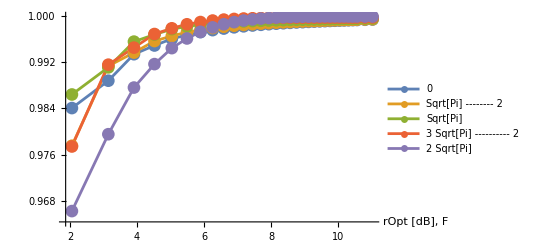

```mathematica
Plot1 = Table[{10*Log10[Exp[2*1/2*ArcSech[(2*Pi)/SSCToGBSpδFidelityTable[[ii,1,1]]]]],SSCToGBSpδFidelityTable[[ii,1,3]]},{ii,1,Length[nSpace]}];
Plot2 = Table[{10*Log10[Exp[2*1/2*ArcSech[(2*Pi)/SSCToGBSpδFidelityTable[[ii,2,1]]]]],SSCToGBSpδFidelityTable[[ii,2,3]]},{ii,1,Length[nSpace]}];
Plot3 = Table[{10*Log10[Exp[2*1/2*ArcSech[(2*Pi)/SSCToGBSpδFidelityTable[[ii,2,1]]]]],SSCToGBSpδFidelityTable[[ii,3,3]]},{ii,1,Length[nSpace]}];
Plot4 = Table[{10*Log10[Exp[2*1/2*ArcSech[(2*Pi)/SSCToGBSpδFidelityTable[[ii,2,1]]]]],SSCToGBSpδFidelityTable[[ii,4,3]]},{ii,1,Length[nSpace]}];
Plot5 = Table[{10*Log10[Exp[2*1/2*ArcSech[(2*Pi)/SSCToGBSpδFidelityTable[[ii,2,1]]]]],SSCToGBSpδFidelityTable[[ii,5,3]]},{ii,1,Length[nSpace]}];
ListPlot[{Plot1,Plot2,Plot3,Plot4,Plot5},Joined->True,PlotRange->Full,PlotMarkers->{"●",Medium},AxesLabel->{"rOpt [dB]"," F"},PlotLegends->Table[ToString[pSpace[[ii]]],{ii,1,Length[pSpace]}]]
```

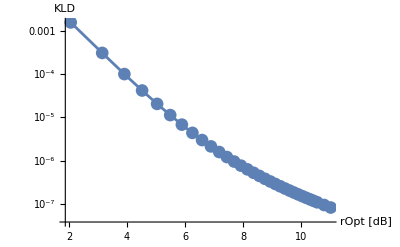

```mathematica
Plot6 = Table[{10*Log10[Exp[2*1/2*ArcSech[(2*Pi)/KLDTable[[ii,1]]]]],KLDTable[[ii,2]]},{ii,1,Length[nSpace]}];
ListLogPlot[Plot6,Joined->True,PlotRange->Full,PlotMarkers->{"●",Medium},AxesLabel->{"rOpt [dB]"," KLD"}]
```